# Z-Scan Simulation using Gaussian Beam Propagation

## Overview

This notebook simulates the Z-scan technique using Gaussian beam propagation and a Kerr medium.

## 1. Physical constants and parameters

This section defines all physical, optical, and numerical parameters used in the Z-scan simulation.

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*=======Beam and laser parameters=======*)
λ=800*10^-9 ;           (*Wavelength[m]*)
ω0=0.4*10^-3;        (*Initial beam waist[m]*)
p=100*10^3;            (*Laser power[W]*)


(*=======Optical system parameters=======*)
f=0.13 ;                         (*Lens focal length[m]*)
d=1*10^-3;                 (*Kerr medium thickness[m]*)
n0=1.76;                        (*Linear refractive index*)
n2=3*10^-3;              (*Nonlinear refractive index[m^2/W]*)


(*=======Scan parameters=======*)
z0=-0.05;                     (*Initial z position[m]*)
zf=0.05;                        (*Final z position[m]*)
nSteps=200;                 (*Number of scan points*)


(*=======Detector parameters=======*)
Rdet=0.5*ω0;           (*Aperture radius[m]*)


(*=======Derived quantities=======*)
I0[w_]:=2 p/(π w^2);  (*Peak intensity*)
q0=-I π ω0^2 n0/λ       (*Initial complex beam parameter*)
```

0.-1.10584 ⅈ

## 2. ABCD matrices

```mathematica
FreeSpace[L_]:={{1,L},{0,1}};

ThinLens[f_]:={{1,0},{-1/f,1}};

Interface[n1_,n2_]:={{1,0},{0,n1/n2}};

KerrLens[z_,w_]:=Module[{hk2},hk2=(8n2 p)/(n0 π w^4);
{{1,d},{-hk2 d,1}}];
```

## 3. Gaussian beam propagation utilities

```mathematica
qPropagate[q_,M_]:=(M[[1,1]] q+M[[1,2]])/(M[[2,1]] q+M[[2,2]]);


BeamWaist[q_]:=Sqrt[-λ/(π n0 *Im[1/q])];
```

## 4. Power through aperture

```mathematica
DetectedPower[w_]:=p (1-Exp[-2 Rdet^2/w^2]);
```

## 5. Test case: single thin lens

```mathematica
LensOnly[z_]:=Module[{M,qf},M=FreeSpace[z].ThinLens[f].FreeSpace[f];
qf=qPropagate[q0,M];
BeamWaist[qf]];


zVals=Subdivide[z0,zf,nSteps];
waistLens=LensOnly/@zVals;
```

## 6. Z-scan simulation with Kerr medium

```mathematica
ZScan[z_]:=Module[{Mpre,qIn,wIn,hk2,Mkerr,Mtot,qDet,wDet},(*------------------------------------------------*)(*Propagation up to the Kerr medium (4 matrices)*)(*------------------------------------------------*)Mpre=Interface[1,n0].FreeSpace[L2[z]].ThinLens[f].FreeSpace[L1];
qIn=qPropagate[q0,Mpre];
wIn=BeamWaist[qIn];
(*------------------------------------------------*)(*Kerr parameter evaluated INSIDE the medium*)(*------------------------------------------------*)hk2=(n0 π wIn^4)/(n2 p);
Mkerr={{1,d},{-1/hk2 d,1}};
(*------------------------------------------------*)(*Full propagation to detector*)(*------------------------------------------------*)Mtot=FreeSpace[L3].Interface[n0,1].Mkerr.Mpre;
qDet=qPropagate[q0,Mtot];
wDet=BeamWaist[qDet];
{wDet,DetectedPower[wDet]}];



zData=ZScan/@zVals;
waistZ=zData[[All,1]];
powerZ=zData[[All,2]];
```

## 7. Plots

```mathematica
zVals;
```

```mathematica
waistLens;
waistZ//N
```

{0.000380377 √(-1./Im[(1.76 (0.568182-4.37063 L1)-1-4.56159×10^12 1^2 (1))/((0.568182-4.37063 L1) (0.001+1.76 L3)-1+(1.-1) (1))]),0.000380377 √(-1./Im[1/1]),0.000380377 √(-1./Im[1]),195,23 1,0.000380377 √(-1./Im[1/1]),0.000380377 √(-1./Im[(1.76 (1)-1-1)/1])}
 |  |  |  |

```mathematica
ListPlot[Transpose[{zVals,waistLens}],AxesLabel->{"z [m]","ω [m]"},PlotLabel->"Beam waist – thin lens"]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{zVals,waistZ}],AxesLabel->{"z [m]","ω [m]"},PlotLabel->"Beam waist – Z-scan"]
```

-Graphics-

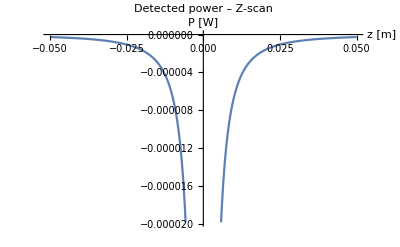

```mathematica
ListLinePlot[Transpose[{zVals,powerZ}],AxesLabel->{"z [m]","P [W]"},PlotLabel->"Detected power – Z-scan"]
```